## PackageName` Documentation

## Preamble

In this section the requirements needed for PackageName` are described, if any, and any necessary Need commands are called.

```mathematica
Needs["PackageName`"]
```

The following packages are needed to run some code found in this documentation notebook.

```mathematica
Needs["OtherPackage`"]
```

## Introduction and Overview

In this section the purpose of PackageName` is described at a high level. It need not be terse (though could be for a simple package) and can include interesting/motivating/cool demonstrative examples.

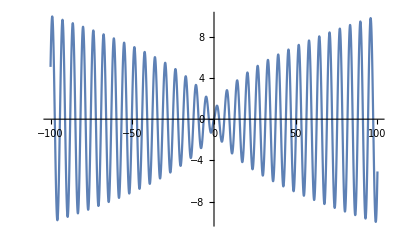

```mathematica
Plot[Sin[x]Sqrt[Abs[x]],{x,-100,100}]
```

## Section One

These sections (at the alt-4 level) enclose a collection of related features in PackageName`. Optionally include an overview of this section. For a simple package, only one section may be necessary, in which case it can be named “Documentation”. Otherwise, its name should be descriptive of its content.

Make sure to close these sections and subsections after you edit and save them, so that they are closed when the next person opens up this document. Delete this cell in a real documentation notebook.

For a very long or complicated package, this section can contain a list of hyperlinks to other notebooks. See dev-guide/DocTools-usage.nb for some details on this.

If a package mainly exposes one or two powerful functions with tons of options, it is appropriate to give an overview of that function here, where each feature describes an option or something like that.

### Feature 1

A feature is a single function or a group of very closely related functions from PackageName`. If a single function, name it the same as the function, otherwise, give a descriptive name.

Include the usage string for each function here, eg:

```mathematica
?KroneckerProduct
?MinimalBy
```

RowBox[{"KroneckerProduct", "[", RowBox[{SubscriptBox[StyleBox["m", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["m", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] constructs the Kronecker product of the arrays SubscriptBox[StyleBox["m", "TI"], StyleBox["i", "TI"]].

MinimalBy[{e_1,e_2,…},f] returns a list of the e_i for which the value of f[e_i] is minimal.
MinimalBy[{e_1,e_2,…},f,n] returns a list of the e_i corresponding to the n smallest f[e_i].
MinimalBy[f] represents an operator form of MinimalBy that can be applied to an expression.

#### Options

If the function has options, enumerate and/or describe them here. If the options have usage text, use the DisplayOptions function provided by DocTools` as demonstrated below. If options are complicated, enumerate them here, but provide an example in a later section.

```mathematica
DisplayOptions[NDSolve]
```

Option | Default Value | Description
AccuracyGoal | Automatic | AccuracyGoal is an option for various numerical operations which specifies how many effective digits of accuracy should be sought in the final result. 
Compiled | Automatic | Compiled is an option for various numerical and plotting functions which specifies whether the expressions they work with should automatically be compiled. 
DependentVariables | Automatic | DependentVariables is an option for NDSolve and other functions that specifies the list of all objects that should be considered as dependent variables in equations that have been supplied.
DiscreteVariables | {} | DiscreteVariables is an option for NDSolve and other functions that specifies variables that only change at discrete times in a temporal integration.
EvaluationMonitor | None | EvaluationMonitor is an option for various numerical computation and plotting functions that gives an expression to evaluate whenever functions derived from the input are evaluated numerically. 
InterpolationOrder | Automatic | InterpolationOrder is an option for Interpolation, as well as ListLinePlot, ListPlot3D, ListContourPlot, and related functions, that specifies what order of interpolation to use.
MaxStepFraction | 1/10 | MaxStepFraction is an option to functions like NDSolve that specifies the maximum fraction of the total range to cover in a single step.
MaxSteps | Automatic | MaxSteps is an option to functions like NDSolve that specifies the maximum number of steps to take in generating a result.
MaxStepSize | Automatic | MaxStepSize is an option to functions like NDSolve that specifies the maximum size of a single step used in generating a result.
Method | Automatic | Method is an option for various algorithm-intensive functions that specifies what internal methods they should use.
NormFunction | Automatic | NormFunction is an option for functions such as FindFit and NDSolve which gives a function to be minimized in generating results.
PrecisionGoal | Automatic | PrecisionGoal is an option for various numerical operations which specifies how many effective digits of precision should be sought in the final result. 
StartingStepSize | Automatic | StartingStepSize is an option to NDSolve and related functions that specifies the initial step size to use in trying to generate results.
StepMonitor | None | StepMonitor is an option for iterative numerical computation functions that gives an expression to evaluate whenever a step is taken by the numerical method used. 
WorkingPrecision | MachinePrecision | WorkingPrecision is an option for various numerical operations that specifies how many digits of precision should be maintained in internal computations.

#### Example 1

An example of the functions above.

#### Example 2

Another example of the functions above.

### Feature 2

Same as feature 1, etc., etc.

## Section Two

Same as Section One, etc., etc.